```mathematica
H[t_]:=Sqrt[1+t^2];
θ[t_]:=ArcCos[t/Sqrt[1+t^2]];
$Assumptions=Element[{t},Reals];
αs={1};
βs={0};
Clear[α];
α[t_]:=1;
Do[α[t_]=Integrate[(-I/(2*H[t]))*(((1/4)*(D[θ[t],t])^2 * α[t])+D[α[t],{t,2}] - ((D[θ[t],{t,2}]/D[θ[t],t])*D[α[t],t])),t];
β[t_]:=-2*D[α[t],t]/D[θ[t],t];
AppendTo[αs,α[t]];
AppendTo[βs,β[t]],
{i,5}]
bbs[t]
```

{{1. Cos[1/2 ArcCos[t/(√(1+t^2))]]+0.3018 (-(ⅈ t (3+2 t^2) Cos[1/2 ArcCos[t/(√(1+t^2))]])/(24 (1+t^2)^(3/2))+(2 √(1-t^2/(1+t^2)) (-(ⅈ t^2)/(6 (1+t^2)^(3/2))+(ⅈ t^2 (3+2 t^2))/(8 (1+t^2)^(5/2))-(ⅈ (3+2 t^2))/(24 (1+t^2)^(3/2))) Sin[1/2 ArcCos[t/(√(1+t^2))]])/(-t^2/((1+t^2)^(3/2))+1/(√(1+t^2))))+0.0910832 (((-32+3 t^2) Cos[1/2 ArcCos[t/(√(1+t^2))]])/(1152 (1+t^2)^3)+(2 √(1-t^2/(1+t^2)) (t/(192 (1+t^2)^3)-(t (-32+3 t^2))/(192 (1+t^2)^4)) Sin[1/2 ArcCos[t/(√(1+t^2))]])/(-t^2/((1+t^2)^(3/2))+1/(√(1+t^2))))},{1. Sin[1/2 ArcCos[t/(√(1+t^2))]]+0.3018 (-(2 √(1-t^2/(1+t^2)) (-(ⅈ t^2)/(6 (1+t^2)^(3/2))+(ⅈ t^2 (3+2 t^2))/(8 (1+t^2)^(5/2))-(ⅈ (3+2 t^2))/(24 (1+t^2)^(3/2))) Cos[1/2 ArcCos[t/(√(1+t^2))]])/(-t^2/((1+t^2)^(3/2))+1/(√(1+t^2)))-(ⅈ t (3+2 t^2) Sin[1/2 ArcCos[t/(√(1+t^2))]])/(24 (1+t^2)^(3/2)))+0.0910832 (-(2 √(1-t^2/(1+t^2)) (t/(192 (1+t^2)^3)-(t (-32+3 t^2))/(192 (1+t^2)^4)) Cos[1/2 ArcCos[t/(√(1+t^2))]])/(-t^2/((1+t^2)^(3/2))+1/(√(1+t^2)))+((-32+3 t^2) Sin[1/2 ArcCos[t/(√(1+t^2))]])/(1152 (1+t^2)^3))}}

```mathematica
ϵ = 0.3018;
(*uplus[t_]:=Cos[θ[t]/2],Sin[θ[t]/2];
uminus[t_]:=Sin[θ[t]/2],-Cos[θ[t]/2];*)
uplus[t_]:={{Cos[θ[t]/2]},{Sin[θ[t]/2]}};
uminus[t_]:={{Sin[θ[t]/2]},{-Cos[θ[t]/2]}};
bb[n_,nt_]:=(ϵ^(n))*(((αs[[n+1]]/. t->nt)*uplus[nt])+( (βs[[n+1]]/. t->nt)*uminus[nt]));
bbs[nt_]:=Sum[bb[n,nt],{n,0,2}];
Qs = Table[Flatten[{nt,{ConjugateTranspose[bbs[ϵ*nt]].{{0,-I},{I,0}}.bbs[ϵ*nt]}}],{nt,-4+0.0001,4.0001,0.01}];
Rs = Table[Flatten[{nt,{ConjugateTranspose[bbs[ϵ*nt]].{{0,1},{1,0}}.bbs[ϵ*nt]}}],{nt,-4+0.0001,4.0001,0.01}];
Ss = Table[Flatten[{nt,{ConjugateTranspose[bbs[ϵ*nt]].{{1,0},{0,-1}}.bbs[ϵ*nt]}}],{nt,-4+0.0001,4.0001,0.01}];
XYs = Table[Flatten[{{ConjugateTranspose[bbs[ϵ*nt]].{{0,1},{1,0}}.bbs[ϵ*nt]},{ConjugateTranspose[bbs[ϵ*nt]].{{0,-I},{I,0}}.bbs[ϵ*nt]}}],{nt,-4+0.0001,4.0001,0.01}];
```

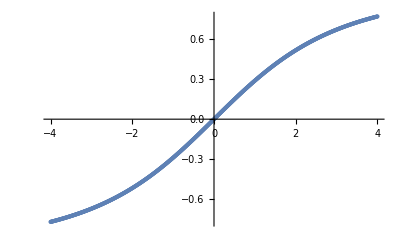

```mathematica
ListPlot[Ss]
```

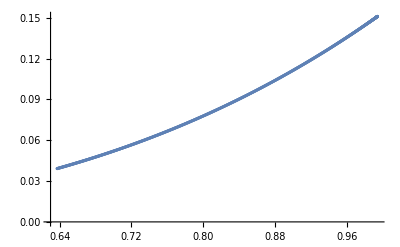

```mathematica
ListPlot[XYs]
```

```mathematica
ParametricPlot3D[Flatten[{ConjugateTranspose[bbs[u]].{{0,1},{1,0}}.bbs[u],ConjugateTranspose[bbs[u]].{{0,-I},{I,0}}.bbs[u],ConjugateTranspose[bbs[u]].{{1,0},{0,-1}}.bbs[u]}],{u,-2,2}]
```

-Graphics3D-

```mathematica
XYZs = Table[Flatten[{{ConjugateTranspose[bbs[ϵ*nt]].{{0,1},{1,0}}.bbs[ϵ*nt]},{ConjugateTranspose[bbs[ϵ*nt]].{{0,-I},{I,0}}.bbs[ϵ*nt]},
{ConjugateTranspose[bbs[ϵ*nt]].{{1,0},{0,-1}}.bbs[ϵ*nt]}
}],{nt,-4+0.0001,4.0001,0.1}];
```

```mathematica
SdotE=(#.Table[PauliMatrix[k],{k,3}]&/@XYZs);
```

```mathematica
σ[t_]:=Integrate[2*Sqrt[1+(ϵ*dt)^2],{dt,0,t}]/Sqrt[2*ϵ*(Pi/2)];
σs =Table[σ[t],{t,-4+0.0001,4.0001,0.1}];
```

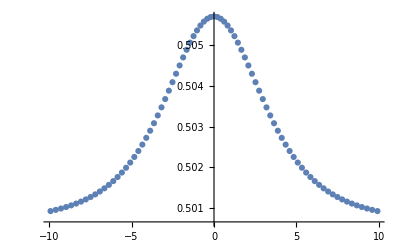

```mathematica
ntRange=Range[-4+0.0001,4.0001,0.1];
results=MapThread[Function[{nt,SdotEValue,sig},Flatten[{sig,{ConjugateTranspose[bbs[ϵ*nt]].SdotEValue.bbs[ϵ*nt]}/2}]],{ntRange,SdotE,σs}];
yValue=1-0.0055;
(*points=Table[{x,yValue},{x,-10,10,0.1}];
p1= ListLinePlot[points,PlotRange->{{-4,4},{yValue-0.01,yValue+0.01}}];*)
p2 = ListPlot[results//Chop];
Show[p2]
```

```mathematica
results
```

{{-9.91214,1.00046+2.1674×10^-19 ⅈ},{-9.59255,1.00048-4.33473×10^-19 ⅈ},{-9.27768,1.0005-6.50199×10^-19 ⅈ},{-8.96748,1.00051+6.50188×10^-19 ⅈ},{-8.6619,1.00053-8.66899×10^-19 ⅈ},{-8.36087,1.00056-2.1672×10^-19 ⅈ},{-8.06435,1.00058+8.66859×10^-19 ⅈ},{-7.77227,1.00061+2.16709×10^-19 ⅈ},{-7.48457,1.00064-4.33405×10^-19 ⅈ},{-7.20117,1.00067-1.08348×10^-18 ⅈ},{-6.922,1.0007+8.66751×10^-19 ⅈ},{-6.64699,1.00074+4.33359×10^-19 ⅈ},{-6.37607,1.00079+0. ⅈ},{-6.10915,1.00083+0. ⅈ},{-5.84614,1.00088-4.33299×10^-19 ⅈ},{-5.58696,1.00094+8.6655×10^-19 ⅈ},{-5.33151,1.001+1.29975×10^-18 ⅈ},{-5.0797,1.00106-4.33222×10^-19 ⅈ},{-4.83142,1.00113-1.29958×10^-18 ⅈ},{-4.58657,1.0012+0. ⅈ},{-4.34504,1.00128+0. ⅈ},{-4.10671,1.00136-1.73236×10^-18 ⅈ},{-3.87146,1.00145+0. ⅈ},{-3.63918,1.00154+8.66027×10^-19 ⅈ},{-3.40972,1.00164+8.65944×10^-19 ⅈ},{-3.18295,1.00174-8.65858×10^-19 ⅈ},{-2.95875,1.00184-8.65771×10^-19 ⅈ},{-2.73695,1.00194+1.73136×10^-18 ⅈ},{-2.51742,1.00205+8.65592×10^-19 ⅈ},{-2.3,1.00215+8.65502×10^-19 ⅈ},{-2.08453,1.00225+0. ⅈ},{-1.87085,1.00235+8.65329×10^-19 ⅈ},{-1.6588,1.00244+8.65249×10^-19 ⅈ},{-1.4482,1.00253+1.73035×10^-18 ⅈ},{-1.23888,1.00261+0. ⅈ},{-1.03066,1.00268-1.73009×10^-18 ⅈ},{-0.823375,1.00274+3.45997×10^-18 ⅈ},{-0.616828,1.00279-3.4598×10^-18 ⅈ},{-0.410839,1.00282+0. ⅈ},{-0.205223,1.00284+0. ⅈ},{0.000205398,1.00285+0. ⅈ},{0.205634,1.00284+0. ⅈ},{0.41125,1.00282+1.72984×10^-18 ⅈ},{0.61724,1.00279+1.7299×10^-18 ⅈ},{0.823789,1.00274-1.72998×10^-18 ⅈ},{1.03108,1.00268+0. ⅈ},{1.2393,1.00261+0. ⅈ},{1.44862,1.00253-3.46069×10^-18 ⅈ},{1.65922,1.00244+2.59575×10^-18 ⅈ},{1.87128,1.00235+0. ⅈ},{2.08496,1.00225+8.65415×10^-19 ⅈ},{2.30043,1.00215-8.65502×10^-19 ⅈ},{2.51786,1.00204-8.65592×10^-19 ⅈ},{2.73739,1.00194-8.65682×10^-19 ⅈ},{2.95919,1.00184+1.73154×10^-18 ⅈ},{3.1834,1.00174-8.65859×10^-19 ⅈ},{3.41017,1.00164+8.65944×10^-19 ⅈ},{3.63964,1.00154-8.66027×10^-19 ⅈ},{3.87193,1.00145+8.66106×10^-19 ⅈ},{4.10718,1.00136+1.73236×10^-18 ⅈ},{4.34552,1.00128+4.33127×10^-18 ⅈ},{4.58706,1.0012+1.73264×10^-18 ⅈ},{4.83191,1.00113+8.66385×10^-19 ⅈ},{5.0802,1.00106+0. ⅈ},{5.33202,1.001+1.29975×10^-18 ⅈ},{5.58747,1.00094+0. ⅈ},{5.84666,1.00088+8.66598×10^-19 ⅈ},{6.10968,1.00083-4.33321×10^-19 ⅈ},{6.37661,1.00079+0. ⅈ},{6.64754,1.00074-8.66718×10^-19 ⅈ},{6.92255,1.0007+8.66751×10^-19 ⅈ},{7.20173,1.00067-8.66782×10^-19 ⅈ},{7.48514,1.00064-1.08351×10^-18 ⅈ},{7.77285,1.00061-4.33418×10^-19 ⅈ},{8.06494,1.00058-2.16715×10^-19 ⅈ},{8.36147,1.00056-2.1672×10^-19 ⅈ},{8.6625,1.00053+8.66899×10^-19 ⅈ},{8.96809,1.00051+1.08365×10^-18 ⅈ},{9.2783,1.0005+2.16733×10^-19 ⅈ},{9.59318,1.00048-3.25105×10^-19 ⅈ},{9.91279,1.00046-3.2511×10^-19 ⅈ}}

```mathematica
-Conjugate[(ⅈ (-t^2/((1+t^2)^(3/2))+1/(√(1+t^2))))/(4 √(1+t^2) √(1-t^2/(1+t^2)))]*(-(ⅈ t (3+2 t^2))/(24 (1+t^2)^(3/2))+1)//Simplify
```

{{0.000346777-0.000692559 ⅈ}}

```mathematica
ConjugateTranspose[bbs[100]].bbs[100]//FullSimplify
```

{{1.00063+0. ⅈ}}